### Map Making Functions

```mathematica
arraymapmaker[order_,initialjitter1_,initialjitter2_,jitterfunction1_,jitterfunction2_,read_,filename_]:=Module[{size,base,mid,map,new,dimlist,squarecorners,diamondcorners,dim,file,jitter1,jitter2,initialjitter,cornerx,cornery},

size=2^order+1;
initialjitter:=RandomReal[{initialjitter1,initialjitter2}];
map=SparseArray[{{1,1}->initialjitter,{size,size-1}->0,{1,size-1}->0,{size,1}->initialjitter}];
mid[n_]:=(n+1)/2;
dimlist=Reverse[Table[2^i+1,{i,1,order}]];
file=filename;

Do[
dim=dimlist[[i]];
squarecorners=Flatten[Table[{y(dim-1)+1,x(dim-1)+1},{y,0,(size-1)/(dim-1)-1,1},{x,0,(size-1)/(dim-1)-1,1}],1];
diamondcorners=DeleteDuplicates[Join[Flatten[Table[{y(dim-1)+1,Mod[x(dim-1)+1,size-1,1]},{y,0,(size-1)/(dim-1),1},{x,0,(size-1)/(dim-1),1}],1],Flatten[Table[{y(dim-1)+1-1+mid[dim],x(dim-1)+1-1+mid[dim]},{y,0,(size-1)/(dim-1)-1,1},{x,0,(size-1)/(dim-1)-1,1}],1]]];
jitter1=jitterfunction1;
jitter2=jitterfunction2;

Do[
cornery=squarecorners[[i,1]];
cornerx=squarecorners[[i,2]];
new=(map[[cornery,cornerx]]+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]+map[[cornery-1+dim,cornerx]]+map[[cornery-1+dim,Mod[cornerx-1+dim,size-1,1]]])/4.+RandomReal[{jitter1,jitter2}];
(map[[cornery-1+mid[dim],cornerx-1+mid[dim]]]=#)&@new;

,{i,1,Length[squarecorners]}];
If[read==1,Export[file,map,"HarwellBoeing"]];
Print["Completed Squares for dimension  "<>ToString[dimlist[[i]]]]

Do[
cornery=diamondcorners[[i,1]];
cornerx=diamondcorners[[i,2]];

If[(cornery-1+mid[dim])>size,(*southpole*)
new=
(map[[cornery,cornerx]]
+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]
(*+map[[cornery+1-mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]]*))
/2.(*+RandomReal[{jitter1,jitter2}]*),

If[cornery+1-mid[dim]≤0,(*northpole*)
new=
(map[[cornery,cornerx]]
+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]
(*+map[[cornery-1+mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]]*))
/2.(*+RandomReal[{jitter1,jitter2}]*),

new=
(map[[cornery,cornerx]]
+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]
+map[[cornery-1+mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]]
+map[[cornery+1-mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]])
/4.+RandomReal[{jitter1,jitter2}]]];
(map[[cornery,Mod[cornerx-1+mid[dim],size-1,1]]]=#)&@new;
,
{i,1,Length[diamondcorners]}];
If[read==1,Export[file,map,"HarwellBoeing"]];
Print["Completed dimension "<>ToString[dimlist[[i]]]<>" of "<>ToString[dimlist]<>" at "<>ToString[DateString[]]],
{i,1,Length[dimlist]}];
]
```

```mathematica
arraymapmaker21[order_,initialjitter1_,initialjitter2_,jitterfunction1_,jitterfunction2_,read_,filename_]:=Module[{size,halfsize,base,mid,map,new,dimlist,squarecorners,diamondcorners,dim,file,jitter1,jitter2,initialjitter,cornerx,cornery},

size=2^order+1;
halfsize=(size+1)/2;
initialjitter:=RandomReal[{initialjitter1,initialjitter2}];
map=SparseArray[{{1,1}->initialjitter,{halfsize,size-1}->0,{1,size-1}->0,{halfsize,1}->initialjitter}];
mid[n_]:=(n+1)/2;
dimlist=Reverse[Table[2^i+1,{i,1,order}]];
file=filename;

Do[
dim=dimlist[[i]];
squarecorners=Flatten[Table[{y(dim-1)+1,x(dim-1)+1},{y,0,(halfsize-1)/(dim-1)-1,1},{x,0,(size-1)/(dim-1)-1,1}],1];
diamondcorners=DeleteDuplicates[Join[Flatten[Table[{y(dim-1)+1,Mod[x(dim-1)+1,size-1,1]},{y,0,(halfsize-1)/(dim-1),1},{x,0,(size-1)/(dim-1),1}],1],Flatten[Table[{y(dim-1)+1-1+mid[dim],x(dim-1)+1-1+mid[dim]},{y,0,(halfsize-1)/(dim-1)-1,1},{x,0,(size-1)/(dim-1)-1,1}],1]]];
jitter1=jitterfunction1;
jitter2=jitterfunction2;
Do[
cornery=squarecorners[[i,1]];
cornerx=squarecorners[[i,2]];
new=(map[[cornery,cornerx]]+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]+map[[cornery-1+dim,cornerx]]+map[[cornery-1+dim,Mod[cornerx-1+dim,size-1,1]]])/4.+(RandomChoice[{-1,1}]*RandomReal[{jitter1,jitter2}]);
(map[[cornery-1+mid[dim],cornerx-1+mid[dim]]]=#)&@new;

,{i,1,Length[squarecorners]}];
If[read==1,Export[file,map,"HarwellBoeing"]];
Print["Completed Squares for dimension  "<>ToString[dimlist[[i]]]]

Do[
cornery=diamondcorners[[i,1]];
cornerx=diamondcorners[[i,2]];

If[(cornery-1+mid[dim])>halfsize,(*southpole*)
new=
(map[[cornery,cornerx]]
+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]
(*+map[[cornery+1-mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]]*))
/2.(*+RandomReal[{jitter1,jitter2}]*),

If[cornery+1-mid[dim]≤0,(*northpole*)
new=
(map[[cornery,cornerx]]
+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]
(*+map[[cornery-1+mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]]*))
/2.(*+RandomReal[{jitter1,jitter2}]*),

new=
(map[[cornery,cornerx]]
+map[[cornery,Mod[cornerx-1+dim,size-1,1]]]
+map[[cornery-1+mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]]
+map[[cornery+1-mid[dim],Mod[cornerx-1+mid[dim],size-1,1]]])
/4.+(RandomChoice[{-1,1}]*RandomReal[{jitter1,jitter2}])]];
(map[[cornery,Mod[cornerx-1+mid[dim],size-1,1]]]=#)&@new;
,
{i,1,Length[diamondcorners]}];
If[read==1,Export[file,map,"HarwellBoeing"]];
Print["Completed dimension "<>ToString[dimlist[[i]]]<>" of "<>ToString[dimlist]<>" at "<>ToString[DateString[]]],
{i,1,Length[dimlist]}];
]
```

### Color Functions

```mathematica
cf1=If[#<0.2,ColorData["DarkTerrain"][0.08],If[#<0.3,ColorData["DarkTerrain"][0.1],If[#>0.9,ColorData["DarkTerrain"][0.95],"DarkTerrain"~Blend~#]]]&;

cf2mask=If[#<0.3,Black,If[#>0.5&&#<0.55,Black,If[#>0.7&&#<0.73,Black,White]]]&;
cf2=If[#<0.2,ColorData["DarkTerrain"][0.08],If[#<0.3,ColorData["DarkTerrain"][0.1],If[#>0.9,ColorData["DarkTerrain"][0.95],If[#>0.5&&#<0.55,ColorData["DarkTerrain"][0.1],If[#>0.7&&#<0.73,ColorData["DarkTerrain"][0.1],"DarkTerrain"~Blend~#]]]]]&;


cf3=If[#<0.2,ColorData["DarkTerrain"][0.08],
If[#<0.28,ColorData["DarkTerrain"][0.1],
If[#<0.3,ColorData["DarkTerrain"][0.12],
If[#>0.95,ColorData["AlpineColors"][0.95],
If[#>0.51&&#<0.54,ColorData["DarkTerrain"][0.1],
If[#>0.50&&#<0.55,ColorData["DarkTerrain"][0.12],
If[#>0.71&&#<0.72,ColorData["DarkTerrain"][0.1],
If[#>0.7&&#<0.73,ColorData["DarkTerrain"][0.12],
If[#>0.56&&#<0.69,"DarkTerrain"~Blend~(1-#),
If[#>0.85&&#<0.95,"AlpineColors"~Blend~#,
"DarkTerrain"~Blend~#]]]]]]]]]]&;

cf4=If[#<0.2,ColorData["DarkTerrain"][0.08],
If[#<0.28,ColorData["DarkTerrain"][0.1],
If[#<0.3,ColorData["DarkTerrain"][0.12],
If[#>0.95,ColorData["AlpineColors"][0.95],
If[#>0.56&&#<0.69,"DarkTerrain"~Blend~(1-#),
If[#>0.85&&#<0.95,"AlpineColors"~Blend~#,
"DarkTerrain"~Blend~#]]]]]]&;
cf5=If[#<0.15,ColorData["DarkTerrain"][0.08],
If[#<0.2,ColorData["DarkTerrain"][0.1],
If[#<0.23,ColorData["DarkTerrain"][0.12],
"CoffeeTones"~Blend~(1-#)]]]&;
cf7=Function[x,Blend[Transpose[{{0,0.2,0.25,.3,0.5,0.7,0.9,1.0},{ColorData["DarkTerrain"][0.08],ColorData["DarkTerrain"][0.08],ColorData["DarkTerrain"][0.25],ColorData["DarkTerrain"][0.3],ColorData["DarkTerrain"][0.5],ColorData["DarkTerrain"][0.7],ColorData["DarkTerrain"][0.9],ColorData["DarkTerrain"][.95]}}],x]];

cf8=
If[#<0.6,ColorData["DarkTerrain"][0.06],
If[#<0.7,ColorData["DarkTerrain"][0.12],
"SandyTerrain"~Blend~(#)]]&;


cf9=
If[#<0.5,ColorData["DarkTerrain"][0.06],
If[#<0.6,ColorData["DarkTerrain"][0.12],
"PigeonTones"~Blend~(#)]]&;
cf9m=If[#<0.6,Black,White]&;
cf9b=If[#<0.6,Black,"GrayTones"~Blend~(#)]&;

cf10=If[#<0.15,ColorData["AlpineColors"][0.0],
If[#<0.2,ColorData["AlpineColors"][0.05],
If[#<0.23,ColorData["AlpineColors"][0.08],
"AlpineColors"~Blend~(#)]]]&;
cf11=If[#<0.25,"BlueGreenYellow"~Blend~(#),
"AlpineColors"~Blend~(#/0.5-0.2)]&;
cf11b=If[#<0.25,Black,
"GrayTones"~Blend~(#)]&;

cflist={cf1->"cf1",cf2->"cf2",cf3->"cf3",cf4->"cf4",cf5->"cf5",cf7->"cf7",cf8->"cf8",cf9->"cf9",cf10->"cf10",cf11->"cf11"};
```

### Map Producer

```mathematica
arraymapmaker21[8,-1,1,-100/(i*6)^2,100/(i*6)^2,1,"~/Desktop/map.cua"]
```

Completed Squares for dimension  257

Completed dimension 257 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:10

Completed Squares for dimension  129

Completed dimension 129 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:10

Completed Squares for dimension  65

Completed dimension 65 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:10

Completed Squares for dimension  33

Completed dimension 33 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:10

Completed Squares for dimension  17

Completed dimension 17 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:10

Completed Squares for dimension  9

Completed dimension 9 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:10

Completed Squares for dimension  5

Completed dimension 5 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:10

Completed Squares for dimension  3

Completed dimension 3 of {257, 129, 65, 33, 17, 9, 5, 3} at Tue 14 Jul 2020 16:06:12

```mathematica
map=Import["~/Desktop/map.cua"]
normmap=(map-Min[map])/Max[map-Min[map]];
Manipulate[ArrayPlot[normmap*x+y,Mesh->None,ImageSize->Large,ColorFunctionScaling->False,ColorFunction->color,Frame->False],{{x,1},0.001,1},{y,0,1},{{color,Automatic},cflist}]
```

SparseArray[…]

```mathematica
colormap=cf9;
colormask=cf9m;
colorbump=cf9b;
mapchoice=normmap*0.8+0.1;
```

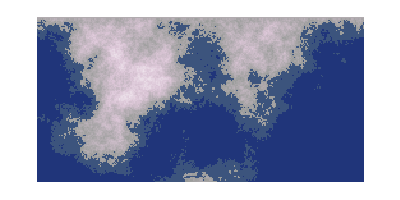

~/Desktop/map.png

-Graphics-

~/Desktop/map_mask.png

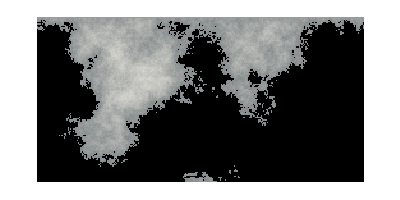

~/Desktop/map_bump.png

```mathematica
mapimage=ArrayPlot[mapchoice,Mesh->None,ColorFunctionScaling->False,ColorFunction->colormap,Frame->False]
Export["~/Desktop/map.png",mapimage,ImageResolution->214]
mapmask=ArrayPlot[mapchoice,Mesh->None,ColorFunctionScaling->False,ColorFunction->colormask,Frame->False]
Export["~/Desktop/map_mask.png",mapmask,ImageResolution->214]
mapbump=ArrayPlot[mapchoice,Mesh->None,ColorFunctionScaling->False,ColorFunction->colorbump,Frame->False]
Export["~/Desktop/map_bump.png",,ImageResolution->214]
```